1

1

2

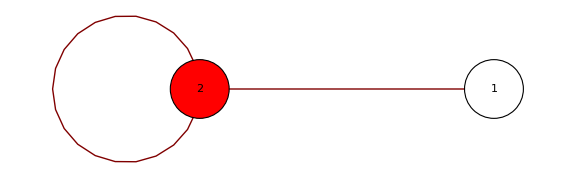

```mathematica
GraphPlot[{{1->2,"1"}, {2->2, "0,1"} }, 
DirectedEdges->True, 
VertexLabeling->True,
VertexRenderingFunction->({ If[#2==2,Red,White],EdgeForm[Black],Print[#2];Disk[#,.1],Black,Text[#2,#1]}&)]
```